```mathematica
Plotter[n1_,n2_]:=Module[{},
a=Import["TEK000"<>n1<>".CSV","Data"];
b=Import["TEK000"<>n2<>".CSV","Data"];
min=Min[Length@a,Length@b];
diff=Last@Last@MovingAverage[a,Length@a]-Last@Last@MovingAverage[b,Length@b];
ListLinePlot[{
{100#[[1]],#[[2]]}&/@((a[[1;;min,{1,2}]]ᵀ-{a[[1,1]],0})ᵀ),
{100#[[1]],#[[2]]}&/@((b[[1;;min,{1,2}]]ᵀ-{a[[1,1]],0})ᵀ)}, PlotRange->All, Frame->True,FrameLabel->{"t [ms]","U [V]"},Axes->False,
PlotLegends->{"Powietrze","Azot"}, AspectRatio->1.5,PlotLabel->"|ΔU|=" <>ToString[ ScientificForm[Abs@diff±(Last@StandardDeviation[a]+Last@StandardDeviation[a])],FormatType->TraditionalForm]]
]
```

## Bez dzielnika

### 72

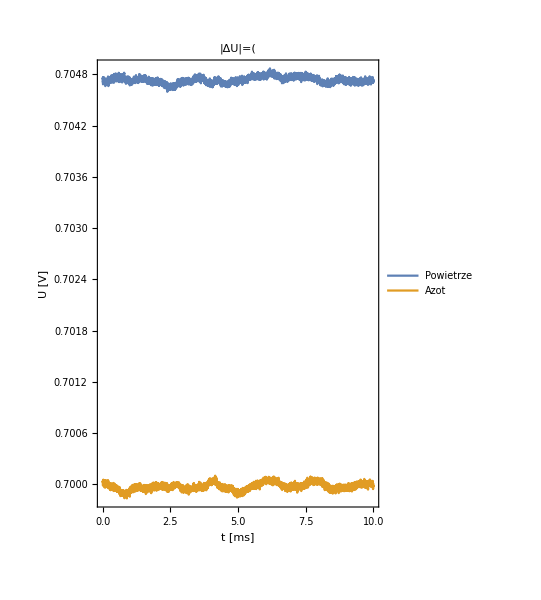

```mathematica
Plotter["01","00"]
```

### 60

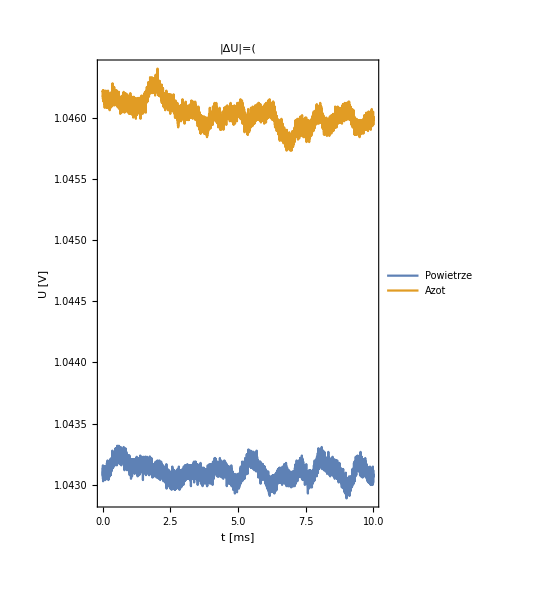

```mathematica
Plotter["02","03"]
```

### 52

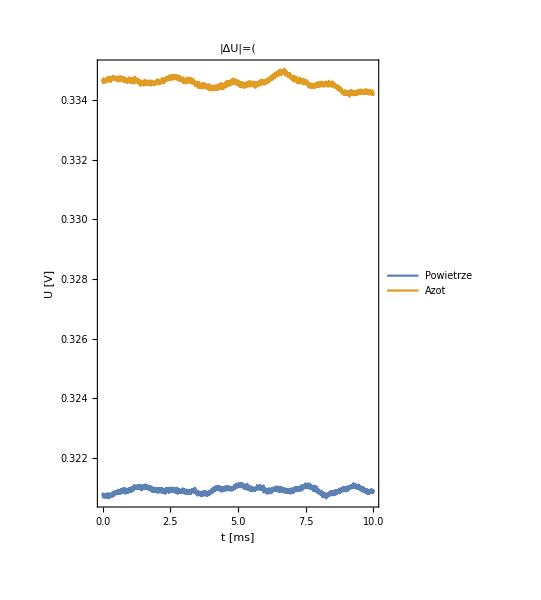

```mathematica
Plotter["04","05"]
```

## Z dzielnikiem

### 60

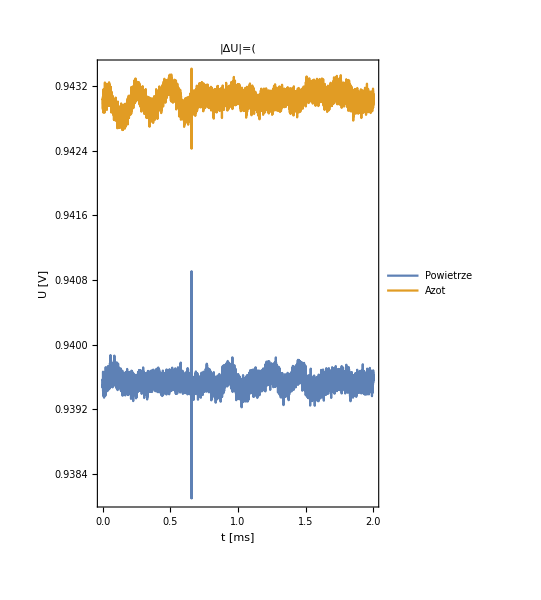

```mathematica
Plotter["10","11"]
```

### 52

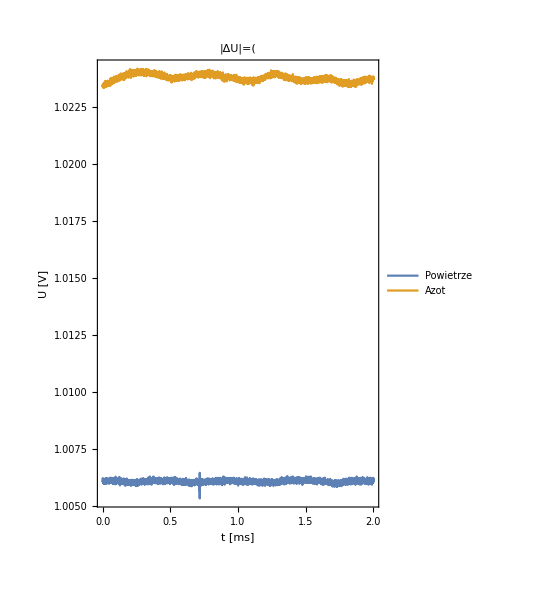

```mathematica
Plotter["12","13"]
```

### 72

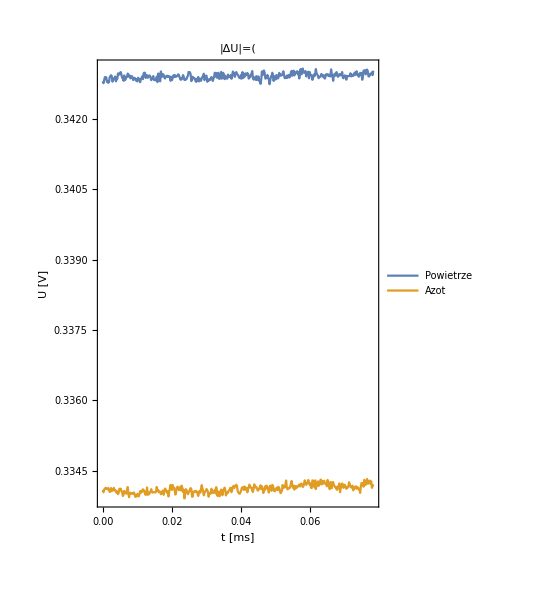

```mathematica
Plotter["14","15"]
```